```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fontsize=28;
```

## Best result up to now

### Plot of low jitter for the Double capillary I took these measurements on 02-15-2021 The jitter is on the order of 3±1 ns

```mathematica
tick=0.04;fontsize=44;
```

```mathematica
data1=Import["low_jitter_double_capillary.csv","Table","FieldSeparators"->{";"}];
t1=Subdivide[-1.2*^-7,1.08*^-6,2000-1];
```

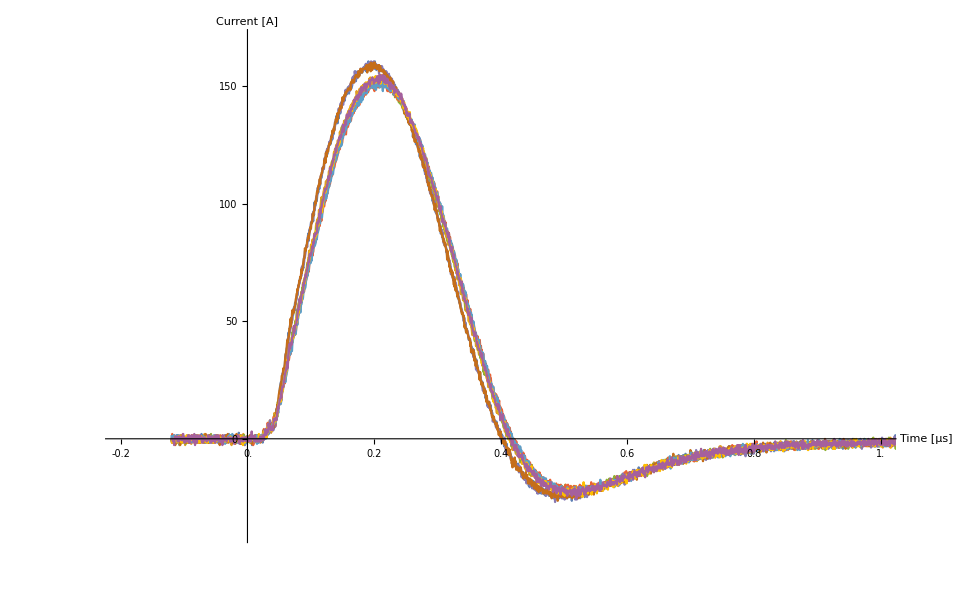

```mathematica
plot1=ListLinePlot[Table[Thread[{t1,data1⟦All,2⟧⟦j*2000+1;;(j+1)*2000⟧}],{j,3,11}]
,PlotStyle->Automatic,
TicksStyle->Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["Time [μs]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
Ticks->{
Table[{j*10^-6,j,tick,Directive[Thick]},{j,-0.2,1,0.2}],
Table[{j,10j,tick,Directive[Thick]},{j,-5,15,5}]
},ImageSize->960,PlotRange->{{-2*10^-7,1*10^-6},{-4,17}}
]
```

```mathematica
Export["low_jitter_curved_capillary.png",plot1]
Export["low_jitter_curved_capillary.pdf",plot1]
```

### Short time window

```mathematica
data=Import["2021-02-10\\1.Wfm.csv","Table","FieldSeparators"->{";"}];
t=Subdivide[-1.5*^-007,8.5*^-007,5000-1];
```

```mathematica
shift=-0.5*10^-7; (*Time interval to shift the axis origin AND the horizonal ticks.*)
```

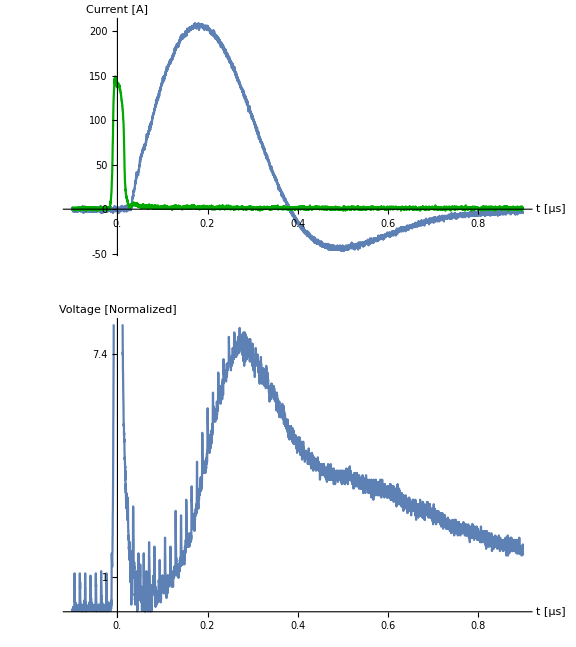

```mathematica
plot1=GraphicsColumn[{
ListLinePlot[{Thread[{t,data⟦All,2⟧}],Style[Thread[{t,3data[[All,1]]}],Darker[Green]]},PlotRange->All
,
Ticks->{Table[{i*10^-7+shift,0.1i,0.04,Thick},{i,0,9,2}], Table[{i,10i,0.04,Thick},{i,-5,20,5}]}
,
TicksStyle->Directive[fontsize,Black]
,
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Current [A]",fontsize,Black]}
,AspectRatio->#,AxesOrigin->{shift,0}]
,
ListLinePlot[{Thread[{t,1.1*data[[All,3]]}]},PlotRange->{0,0.028}
,Ticks->{Table[{i*10^-7+shift,0.1i,0.04,Thick},{i,0,9,2}], {{Max[data[[All,3]]⟦;;200⟧],"1 ",0.04,Thick},{Max[data⟦All,3⟧⟦900;;⟧],NumberForm[Max[data[[All,3]]⟦900;;⟧]/Max[data[[All,3]]⟦;;200⟧],2],0.04,Thick}}}
,
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Voltage\n[Normalized]",fontsize,Black]}
,AspectRatio->#,AxesOrigin->{shift,0}]
}
,ImageSize->Large]&[0.5]
```

```mathematica
Export["curved-pulsetrain-short.png",plot1]
Export["curved-pulsetrain-short.pdf",plot1]
```

### Long time window

```mathematica
data=data=Import["2021-02-10\\2.Wfm.csv","Table","FieldSeparators"->{";"}];
t=Subdivide[-6*^-007,3.4*^-006,10000-1];
```

```mathematica
shift=-0.5*10^-7; (*Time interval to shift the axis origin AND the horizonal ticks.*)
```

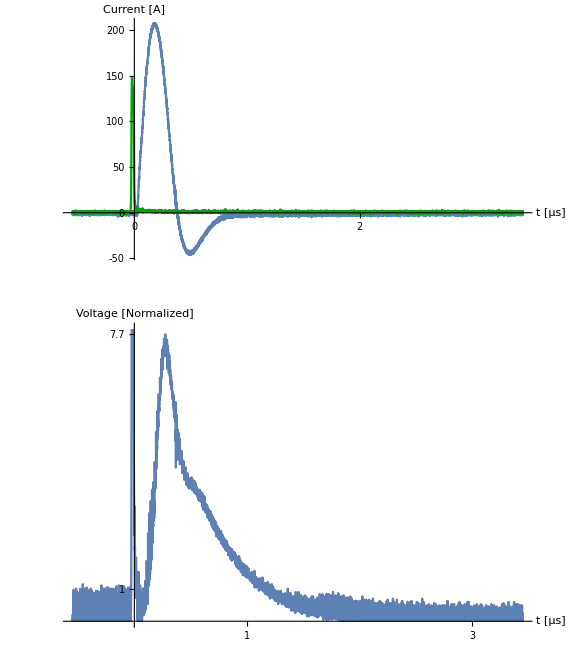

```mathematica
plot2=GraphicsColumn[{
ListLinePlot[{Thread[{t,data[[All,2]]}],Style[Thread[{t,3data[[All,1]]}],Darker[Green]]},PlotRange->All
,
Ticks->{Table[{i*10^-6+shift,i,0.04,Thick},{i,0,9,1}], Table[{i,10i,0.04,Thick},{i,-5,20,5}]}
,
TicksStyle->Directive[fontsize,Black]
,
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Current [A]",fontsize,Black]}
,AspectRatio->#,AxesOrigin->{shift,0}]
,
ListLinePlot[{Thread[{t,data[[All,3]]}]},PlotRange->{0,0.026}
,Ticks->{Table[{i*10^-6+shift,i,0.04,Thick},{i,-1,9,1}], {{Max[data[[All,3]]⟦;;200⟧],"1 ",0.04,Thick},{Max[data[[All,3]]⟦1600;;⟧],NumberForm[Max[data[[All,3]]⟦1600;;⟧]/Max[data[[All,3]]⟦;;1000⟧],2],0.04,Thick}}}
,
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Voltage\n[Normalized]",fontsize,Black]}
,AspectRatio->#,AxesOrigin->{shift,0}]
}
,ImageSize->Large]&[0.5]
```

```mathematica
Export["curved-pulsetrain-long.png",plot2]
Export["curved-pulsetrain-long.pdf",plot2]
```